## Backward lalu Forward

### Backward calculation

```mathematica
Clear["Global`*"]
```

```mathematica
ϵ[p_]=3 p+240. (* Model Quark Star *)
dϵdp=D[ϵ[p],p];
```

240.+3 p

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
```

```mathematica
rmax0=10^(-3);
r00=10720.426841252485;(* radius di permukaan *)
MCC=MSS*1.9608865829552797; (* Massa di permukaan *)
PCC=1.*^-12; (* Tekanan di permukaan *)
```

```mathematica
Clear[rStar2];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r00]==MCC , p[r00]==PCC},{m,p},{r,r00,rmax0},Method->{"EventLocator","Event" :>{r},"EventAction":>Throw[rStar2=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax0]
solb=NDSolve`ProcessSolutions[state]
rStar2
```

{m→InterpolatingFunction[{{0.001, 10720.4}}, <>],p→InterpolatingFunction[{{0.001, 10720.4}}, <>]}

rStar2

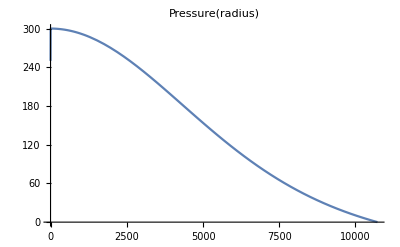

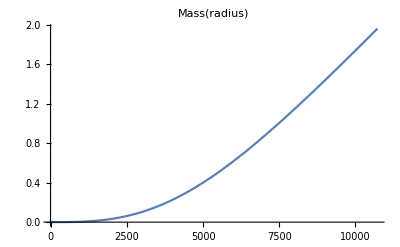

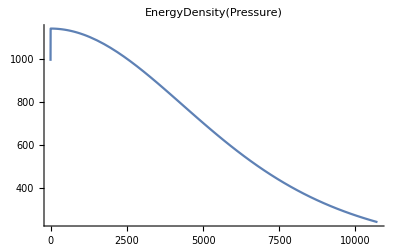

```mathematica
moo[r_]=Evaluate[m[r]/. solb];
poo[r_]=Evaluate[p[r]/. solb];
mStar=moo[rStar];
Plot[{poo[r]},{r,rmax0,r00},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{moo[r]/MSS},{r,rmax0,r00},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[poo[r]]},{r,rmax0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

```mathematica
{rmax0,poo[rmax0],moo[rmax0]/MSS}
{r00,moo[r00]/MSS,poo[r00]}
```

{1/1000,240.423,-3.20266×10^-8}

{10720.4,1.96089,1.×10^-12}

### Reverse calculation

```mathematica
r0=10^(-3);(* radius di pusat *)
rmax=100000.;
MCC=moo[rmax0]; (* Massa di pusat *)
PCC=poo[rmax0]; (* Tekanan di pusat *)
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solf=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 10720.4}}, <>],p→InterpolatingFunction[{{0.001, 10720.4}}, <>]}

10720.4

```mathematica
mo[r_]=Evaluate[m[r]/. solf];
po[r_]=Evaluate[p[r]/. solf];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

10720.428385878211     1.9608866367108606     961.269     240.423

-Graphics-

-Graphics-

-Graphics-

```mathematica
{r0,po[r0],mo[r0]/MSS}
{rStar,mo[rStar]/MSS,po[rStar]}
```

{1/1000,240.423,-3.20266×10^-8}

{10720.4,1.96089,-3.77476×10^-15}

### Perbandingan

```mathematica
(* backward *) 

{rmax0,moo[rmax0]/MSS,poo[rmax0]}
{r00,moo[r00]/MSS,poo[r00]}
```

{1/1000,-3.20266×10^-8,240.423}

{10720.4,1.96089,1.×10^-12}

```mathematica
(* forward *) 

{r0,mo[r0]/MSS,po[r0]}
{rStar,mo[rStar]/MSS,po[rStar]}
```

{1/1000,-3.20266×10^-8,240.423}

{10720.4,1.96089,-3.77476×10^-15}

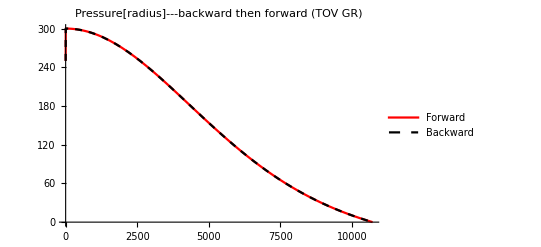

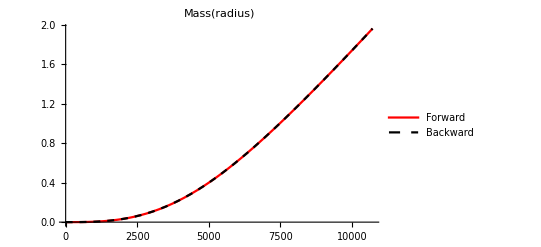

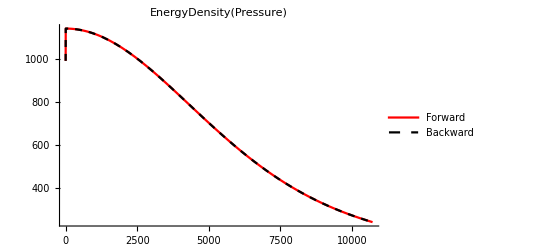

```mathematica
Plot[{po[r],poo[r]},{r,r0,r00},PlotRange->All,PlotLabel->"Pressure[radius]---backward then forward (TOV GR)",PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{mo[r]/MSS,moo[r]/MSS},{r,r0,r00},PlotRange->All,PlotLabel->Mass[radius],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{ϵ[po[r]],ϵ[poo[r]]},{r,r0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
```